```mathematica
(* Import sequences *)

file="True IDR Domains without CRs.fasta";

Header=Import[file,"Header"];
Length[Header]
Seq=Import[file,"Sequence"];
Length[Seq]
```

101

101

```mathematica
(* Analysis loop *)

AnalyseListe={};


(* Load hydro-scale *)
HydroReihenfolge={"W","F","I","L","C","M","V","Y","P","A","T","H","G","S","Q","N","E","D","K","R"};
HydroValue={1.,0.859,0.862,0.8310000000000001,0.782,0.687,0.684,0.604,0.46,0.405,0.39,0.35000000000000003,0.31,0.298,0.242,0.132,0.113,0.012,0.006,0.};
(* Re-scaled values of Table 2 from Pliska and Fauchere, 1983 *)


Monitor[

Do[{holen=Seq[[a]],
NamenHolen=Header[[a]],

DomLength=N[StringLength[holen]],

(* All percentages are normalized according to the full length sequences without GLEBS domain *)

NGly=N[StringCount[holen, "G"]/StringLength[holen]]*100;
NAla=N[StringCount[holen, "A"]/StringLength[holen]]*100;
NVal=N[StringCount[holen, "V"]/StringLength[holen]]*100;
NLeu=N[StringCount[holen, "L"]/StringLength[holen]]*100;
NIle=N[StringCount[holen, "I"]/StringLength[holen]]*100;
NPhe=N[StringCount[holen, "F"]/StringLength[holen]]*100;
NTyr=N[StringCount[holen, "Y"]/StringLength[holen]]*100;
NTrp=N[StringCount[holen, "W"]/StringLength[holen]]*100;
NMet=N[StringCount[holen, "M"]/StringLength[holen]]*100;
NCys=N[StringCount[holen, "C"]/StringLength[holen]]*100;
NSer=N[StringCount[holen, "S"]/StringLength[holen]]*100;
NThr=N[StringCount[holen, "T"]/StringLength[holen]]*100;
NAsn=N[StringCount[holen, "N"]/StringLength[holen]]*100;
NGln=N[StringCount[holen, "Q"]/StringLength[holen]]*100;
NAsp=N[StringCount[holen, "D"]/StringLength[holen]]*100;
NGlu=N[StringCount[holen, "E"]/StringLength[holen]]*100;
NLys=N[StringCount[holen, "K"]/StringLength[holen]]*100;
NR=N[StringCount[holen, "R"]/StringLength[holen]]*100;
NPro=N[StringCount[holen, "P"]/StringLength[holen]]*100;
NHis=N[StringCount[holen, "H"]/StringLength[holen]]*100;


NNQ=NAsn+NGln;
NTS=NThr+NSer;
NDE=NAsp+NGlu;
NRK=NR+NLys;
NDERK=NDE+NRK;
NFILVM=NPhe+NIle+NLeu+NVal+NMet;
NFILVMP=NPhe+NIle+NLeu+NVal+NMet+NPro;

FILVM=AppendTo[FILVM,NFILVM];
FILVMP=AppendTo[FILVMP,NFILVMP];

AbsCharge=((N[StringCount[holen, "R"]]+N[StringCount[holen, "K"]])-(N[StringCount[holen, "D"]]+N[StringCount[holen, "E"]]));
Ladung=(((N[StringCount[holen, "R"]]+N[StringCount[holen, "K"]])+(N[StringCount[holen, "D"]]+N[StringCount[holen, "E"]]))/DomLength);

HydroContributions={};
Do[{HydroContributions=AppendTo[HydroContributions,HydroValue[[x]]*StringCount[holen,HydroReihenfolge[[x]]]]},{x,1,Length[HydroReihenfolge]}],
Hydrophobicity=Total[HydroContributions],

RelativeHydrophobicity=Hydrophobicity/DomLength,

ID=StringJoin["AnalyseMarke_",ToString[a]],


AnalyseEinzelErgebnisse={ID,NamenHolen,
DomLength,
Hydrophobicity,RelativeHydrophobicity,NFILVM,NFILVMP,
AbsCharge,Ladung,NDE,NRK,NDERK,
NGly,NAla,NVal,NLeu,NIle,NPhe,NTyr,NTrp,NMet,NCys,NSer,NThr,NAsn,NGln,NAsp,NGlu,NLys,NR,NPro,NHis,
NNQ,NTS};

AnalyseListe=AppendTo[AnalyseListe,AnalyseEinzelErgebnisse]


},{a,1,Length[Seq]}],ProgressIndicator[a,{1,Length[Sequenzen]}]];

Print["\n",Style["Done!",Bold,Blue],"\n"]
```

Done!

OK

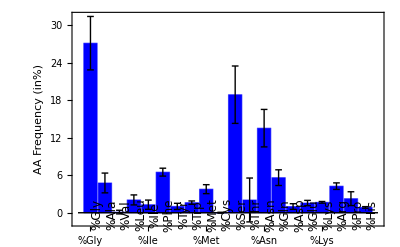

Lfd.-Nr. | Parameter | Mean | StDev | Median | MedianDeviation | Min | Max
3 | Domain length | 119.495 | 7.31659 | 123. | 0. | 93. | 144.
4 | Hydrophobicity | 41.5234 | 2.49457 | 42.226 | 0.196 | 29.266 | 52.103
5 | Hydrophobicity/100aa | 0.347611 | 0.00902097 | 0.344894 | 0.002 | 0.308063 | 0.373991
6 | %FILVM | 13.7212 | 0.646483 | 13.8211 | 0. | 12.1739 | 17.2043
7 | %FILVMP | 15.9765 | 1.35831 | 16.2602 | 0. | 12.6126 | 19.4444
8 | Absolute Charge | 4.0099 | 0.360418 | 4. | 0. | 2. | 6.
9 | Charge/100aa | 0.084728 | 0.00647873 | 0.0813008 | 0. | 0.08 | 0.126316
10 | %DE | 2.54959 | 0.243303 | 2.43902 | 0. | 2.4 | 4.16667
11 | %RK | 5.9232 | 0.491184 | 5.69106 | 0. | 5.55556 | 9.47368
12 | %DERK | 8.4728 | 0.647873 | 8.13008 | 0. | 8. | 12.6316
13 | %Gly | 27.1433 | 4.27502 | 28.4553 | 1.62602 | 16.3462 | 34.0206
14 | %Ala | 4.7674 | 1.58313 | 4.5045 | 1.18655 | 1.05263 | 10.0917
15 | %Val | 0.106431 | 0.292374 | 0. | 0. | 0. | 0.961538
16 | %Leu | 2.05377 | 0.800631 | 1.62602 | 0. | 0.813008 | 4.62963
17 | %Ile | 1.28651 | 0.74128 | 1.62602 | 0. | 0. | 4.16667
18 | %Phe | 6.49836 | 0.632913 | 6.50407 | 0. | 4.62963 | 8.10811
19 | %Tyr | 1.01791 | 0.493965 | 0.813008 | 0. | 0. | 2.77778
20 | %Trp | 1.62041 | 0.266762 | 1.62602 | 0. | 0. | 1.92308
21 | %Met | 3.77609 | 0.717935 | 4.06504 | 0. | 1.73913 | 5.12821
22 | %Cys | 0.00687569 | 0.0690998 | 0. | 0. | 0. | 0.694444
23 | %Ser | 18.8955 | 4.59365 | 17.0732 | 0.813008 | 8.42105 | 30.6306
24 | %Thr | 2.04656 | 3.5104 | 0. | 0. | 0. | 11.5044
25 | %Asn | 13.5396 | 2.99925 | 14.7541 | 0.693056 | 5.55556 | 16.8421
26 | %Gln | 5.6174 | 1.25696 | 5.69106 | 0.813008 | 2.75229 | 9.47368
27 | %Asp | 0.993377 | 0.455654 | 0.813008 | 0. | 0. | 2.15054
28 | %Glu | 1.55621 | 0.423792 | 1.62602 | 0. | 0.819672 | 3.27869
29 | %Lys | 1.66681 | 0.135805 | 1.62602 | 0. | 1.03093 | 2.15054
30 | %Arg | 4.25639 | 0.523891 | 4.06504 | 0. | 3.47222 | 8.42105
31 | %Pro | 2.25538 | 1.10433 | 2.43902 | 0. | 0. | 6.55738
32 | %His | 0.856242 | 0.124945 | 0.813008 | 0. | 0.8 | 1.83486
33 | %NQ | 19.157 | 4.04663 | 21.1382 | 0.813008 | 8.33333 | 26.3158
34 | %TS | 20.9421 | 7.64009 | 17.0732 | 0.813008 | 9.47368 | 40.5405

```mathematica
(* Analyzing the parameter distributions *)

TransposedList=Transpose[AnalyseListe];

TableData={};
ChartData={};

Numerierung=Table[i,{i,Length[labels]}];

labels={"ID","Name",
"Domain length",
"Hydrophobicity","Hydrophobicity/100aa","%FILVM","%FILVMP",
"Absolute Charge","Charge/100aa","%DE","%RK","%DERK",
"%Gly","%Ala","%Val","%Leu","%Ile","%Phe","%Tyr","%Trp","%Met","%Cys","%Ser","%Thr","%Asn","%Gln","%Asp","%Glu","%Lys","%Arg","%Pro","%His",
"%NQ","%TS"};

If[Length[labels]==Length[AnalyseEinzelErgebnisse],Print["OK"],Print[Style["ERROR!",Bold,Red]]]

Do[{mean=Mean[Part[TransposedList,n]],
StDev=StandardDeviation[Part[TransposedList,n]],
median=Median[Part[TransposedList,n]],
MedDev=MedianDeviation[Part[TransposedList,n]],
min=Min[Part[TransposedList,n]],
max=Max[Part[TransposedList,n]],
(* Histo=Histogram[TransposedList[[n]],PlotLabel->Part[labels,n-2]],Print[Histo], *)
TableData=AppendTo[TableData,{Numerierung[[n]],labels[[n]],N[mean],N[StDev],N[median],N[MedDev],N[min],N[max]}],
ChartData=AppendTo[ChartData,{mean->StDev}]},
{n,3,Length[TransposedList]}]

ChartData=Flatten[ChartData];

errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

Bar=BarChart[ChartData[[11;;30]],ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[labels[[13;;32]],Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],Frame->Left,FrameLabel->{None,Style["AA Frequency (in%)",12,FontFamily->"Arial"]},
ChartStyle->Blue]


TableHead={Style["Lfd.-Nr.",Bold],Style["Parameter",Bold],Style["Mean",Bold],Style["StDev",Bold],Style["Median",Bold],Style["MedianDeviation",Bold],Style["Min",Bold],Style["Max",Bold]};
tabelle=TableForm[PrependTo[TableData,TableHead]]
```

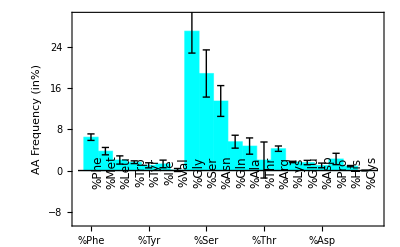

```mathematica
(* Manually re-order the chart data for nice plot *)

NewChartData={
ChartData[[16]],
ChartData[[19]],
ChartData[[14]],
ChartData[[18]],
ChartData[[17]],
ChartData[[15]],
ChartData[[13]],
ChartData[[11]],
ChartData[[21]],
ChartData[[23]],
ChartData[[24]],
ChartData[[12]],
ChartData[[22]],
ChartData[[28]],
ChartData[[27]],
ChartData[[26]],
ChartData[[25]],
ChartData[[29]],
ChartData[[30]],
ChartData[[20]]};

NewLabels={
"%Phe",
"%Met",
"%Leu",
"%Trp",
"%Tyr",
"%Ile",
"%Val",
"%Gly",
"%Ser",
"%Asn",
"%Gln",
"%Ala",
"%Thr",
"%Arg",
"%Lys",
"%Glu",
"%Asp",
"%Pro",
"%His",
"%Cys"
};


BarNeu=BarChart[NewChartData,
ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[NewLabels,Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],
Frame->Left,FrameLabel->{None,Style["AA Frequency (in%)",12,FontFamily->"Arial"]},
ChartStyle->Cyan,
BarSpacing->None,
PlotRange->{Automatic,{-10,30}}]
```

```mathematica
(* Export the data *)

dir=DirectoryName[file];
SetDirectory[dir];
newdir=CreateDirectory["True IDR analysis"];
SetDirectory[newdir];

Export["Statistics summary.pdf",tabelle]
Export["True IDR bar.pdf",BarNeu]
```

Statistics summary.pdf

True IDR bar.pdf